```mathematica
(***Volume of the rectangular solid formed by each counting bin: 50 um length, 821 um width across 6 histological sections per animal***)
```

```mathematica
volume=NIntegrate[Interpolation[Table[N@(50*821*10^-6),{6}]][x],{x,1,6}];(**x10^-6 for mm^3**)
```

```mathematica
(***Corticocortical projection neuron number as a function of depth (50 um bins) from pia for all animals***)
```

```mathematica
allCCcellCountsVsDepth={{{{0,0},{50,0},{100,1},{150,1},{200,1},{250,0},{300,0},{350,0},{400,0},{450,2},{500,8},{550,3},{600,1},{650,1},{700,2},{750,3},{800,8},{850,1},{900,0},{950,0},{1000,0}},{{0,0},{50,0},{100,1},{150,1},{200,0},{250,0},{300,0},{350,0},{400,2},{450,14},{500,4},{550,2},{600,1},{650,3},{700,5},{750,0},{800,2},{850,4},{900,4},{950,0},{1000,0}},{{0,0},{50,0},{100,2},{150,0},{200,1},{250,0},{300,0},{350,4},{400,14},{450,3},{500,1},{550,1},{600,1},{650,0},{700,1},{750,1},{800,2},{850,0},{900,0},{950,0},{1000,0}},{{0,0},{50,0},{100,0},{150,0},{200,1},{250,0},{300,0},{350,0},{400,1},{450,9},{500,2},{550,0},{600,1},{650,4},{700,1},{750,2},{800,0},{850,2},{900,3},{950,0},{1000,0}},{{0,0},{50,0},{100,1},{150,0},{200,0},{250,0},{300,0},{350,0},{400,1},{450,13},{500,1},{550,3},{600,2},{650,1},{700,1},{750,0},{800,3},{850,0},{900,0},{950,0},{1000,0}},{{0,0},{50,0},{100,1},{150,0},{200,0},{250,0},{300,0},{350,0},{400,1},{450,13},{500,9},{550,1},{600,1},{650,3},{700,2},{750,3},{800,0},{850,7},{900,0},{950,0},{1000,0}}},{{{0,0},{50,0},{100,2},{150,2},{200,0},{250,0},{300,0},{350,0},{400,4},{450,11},{500,4},{550,4},{600,5},{650,2},{700,1},{750,1},{800,1},{850,1},{900,0},{950,0},{1000,0}},{{0,0},{50,0},{100,3},{150,2},{200,0},{250,1},{300,0},{350,0},{400,2},{450,22},{500,4},{550,2},{600,5},{650,4},{700,7},{750,2},{800,3},{850,2},{900,2},{950,0},{1000,0}},{{0,0},{50,0},{100,5},{150,0},{200,0},{250,0},{300,0},{350,0},{400,1},{450,12},{500,8},{550,5},{600,2},{650,3},{700,4},{750,3},{800,4},{850,1},{900,0},{950,0},{1000,0}},{{0,0},{50,0},{100,1},{150,1},{200,0},{250,0},{300,0},{350,2},{400,11},{450,14},{500,7},{550,4},{600,5},{650,6},{700,1},{750,1},{800,1},{850,1},{900,0},{950,0},{1000,0}},{{0,0},{50,0},{100,2},{150,0},{200,1},{250,0},{300,0},{350,3},{400,9},{450,13},{500,4},{550,6},{600,0},{650,4},{700,1},{750,1},{800,1},{850,0},{900,0},{950,0},{1000,0}},{{0,0},{50,0},{100,0},{150,0},{200,0},{250,0},{300,0},{350,0},{400,5},{450,8},{500,3},{550,1},{600,1},{650,2},{700,2},{750,7},{800,0},{850,0},{900,0},{950,0},{1000,0}}},{{{0,0},{50,0},{100,0},{150,0},{200,0},{250,0},{300,0},{350,0},{400,0},{450,5},{500,11},{550,2},{600,1},{650,1},{700,2},{750,1},{800,0},{850,0},{900,1},{950,0},{1000,0}},{{0,0},{50,0},{100,1},{150,1},{200,0},{250,0},{300,0},{350,0},{400,0},{450,5},{500,4},{550,4},{600,3},{650,0},{700,0},{750,0},{800,0},{850,1},{900,1},{950,1},{1000,0}},{{0,0},{50,0},{100,0},{150,0},{200,0},{250,0},{300,0},{350,0},{400,0},{450,4},{500,10},{550,2},{600,2},{650,1},{700,0},{750,0},{800,0},{850,0},{900,0},{950,0},{1000,0}},{{0,0},{50,0},{100,0},{150,0},{200,0},{250,0},{300,0},{350,0},{400,0},{450,7},{500,4},{550,3},{600,0},{650,2},{700,1},{750,1},{800,0},{850,0},{900,0},{950,0},{1000,0}},{{0,0},{50,0},{100,0},{150,0},{200,0},{250,0},{300,0},{350,0},{400,0},{450,8},{500,2},{550,0},{600,2},{650,0},{700,1},{750,0},{800,0},{850,1},{900,0},{950,0},{1000,0}},{{0,0},{50,0},{100,0},{150,0},{200,0},{250,0},{300,0},{350,0},{400,2},{450,6},{500,4},{550,0},{600,2},{650,0},{700,0},{750,2},{800,1},{850,1},{900,1},{950,0},{1000,0}}}};
```

```mathematica
ccCellDens=Table[Total[Table[((allCCcellCountsVsDepth[[m]])[[n]])[[All,2]],{n,1,6}]]/volume,{m,1,Length[allCCcellCountsVsDepth]}];
```

```mathematica
meanCC=Mean[ccCellDens];
```

```mathematica
semCC=(#/Sqrt@Length[ccCellDens])&/@StandardDeviation[ccCellDens];
```

```mathematica
v1Color=RGBColor["#ff1f5b"];
```

```mathematica
ccG=ListLinePlot[{meanCC,meanCC+semCC,meanCC-semCC},Filling->{1->{{2},Directive[Opacity[0.4],v1Color]},1->{{3},Directive[Opacity[0.4],v1Color]}},PlotStyle->{{v1Color,Thickness[0.006]},Transparent,Transparent},DataRange->{0,1000},PlotRange->{{0,1000},{0,400}},FrameTicks->{{LinTicks[0,400,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[0,1000,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,Frame->{{True,None},{True,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
(***Corticocortical projection neuron number as a function of depth (50 um bins) from pia for all animals***)
```

```mathematica
allCTcellCountsVsDepth={{{{0,0},{50,0},{100,0},{150,0},{200,0},{250,0},{300,0},{350,0},{400,0},{450,0},{500,1},{550,2},{600,0},{650,0},{700,0},{750,0},{800,0},{850,3},{900,7},{950,0},{1000,0}},{{0,0},{50,0},{100,0},{150,0},{200,0},{250,0},{300,0},{350,0},{400,0},{450,0},{500,1},{550,0},{600,0},{650,0},{700,0},{750,0},{800,0},{850,1},{900,5},{950,6},{1000,0}},{{0,0},{50,0},{100,0},{150,0},{200,0},{250,0},{300,0},{350,0},{400,0},{450,2},{500,1},{550,0},{600,0},{650,1},{700,0},{750,0},{800,0},{850,0},{900,2},{950,6},{1000,10}},{{0,0},{50,0},{100,0},{150,0},{200,0},{250,0},{300,0},{350,0},{400,0},{450,0},{500,0},{550,1},{600,0},{650,0},{700,0},{750,0},{800,7},{850,9},{900,0},{950,0},{1000,0}},{{0,0},{50,0},{100,0},{150,0},{200,0},{250,0},{300,0},{350,0},{400,0},{450,0},{500,2},{550,0},{600,0},{650,0},{700,0},{750,0},{800,0},{850,0},{900,5},{950,5},{1000,1}},{{0,0},{50,0},{100,0},{150,0},{200,0},{250,0},{300,0},{350,0},{400,0},{450,2},{500,1},{550,1},{600,0},{650,0},{700,0},{750,0},{800,1},{850,10},{900,0},{950,0},{1000,0}}},{{{0,0},{50,0},{100,0},{150,0},{200,0},{250,0},{300,0},{350,0},{400,0},{450,0},{500,1},{550,2},{600,0},{650,0},{700,0},{750,0},{800,0},{850,6},{900,1},{950,2},{1000,0}},{{0,0},{50,0},{100,0},{150,0},{200,0},{250,0},{300,0},{350,0},{400,0},{450,0},{500,2},{550,0},{600,0},{650,0},{700,0},{750,0},{800,1},{850,4},{900,5},{950,2},{1000,0}},{{0,0},{50,0},{100,0},{150,0},{200,0},{250,0},{300,0},{350,0},{400,0},{450,0},{500,0},{550,1},{600,1},{650,2},{700,0},{750,0},{800,0},{850,0},{900,3},{950,6},{1000,2}},{{0,0},{50,0},{100,0},{150,0},{200,0},{250,0},{300,0},{350,0},{400,0},{450,0},{500,3},{550,1},{600,0},{650,0},{700,0},{750,2},{800,0},{850,1},{900,1},{950,10},{1000,2}},{{0,0},{50,0},{100,0},{150,0},{200,0},{250,0},{300,0},{350,0},{400,0},{450,0},{500,3},{550,0},{600,0},{650,0},{700,0},{750,0},{800,0},{850,0},{900,6},{950,2},{1000,0}},{{0,0},{50,0},{100,0},{150,0},{200,0},{250,0},{300,0},{350,0},{400,0},{450,3},{500,0},{550,2},{600,0},{650,0},{700,0},{750,1},{800,0},{850,8},{900,1},{950,0},{1000,0}}},{{{0,0},{50,0},{100,0},{150,0},{200,0},{250,0},{300,0},{350,0},{400,0},{450,1},{500,2},{550,0},{600,1},{650,0},{700,0},{750,0},{800,1},{850,8},{900,10},{950,6},{1000,0}},{{0,0},{50,0},{100,0},{150,0},{200,0},{250,0},{300,0},{350,0},{400,1},{450,4},{500,4},{550,0},{600,1},{650,1},{700,4},{750,8},{800,6},{850,10},{900,6},{950,2},{1000,1}},{{0,0},{50,0},{100,0},{150,0},{200,0},{250,0},{300,0},{350,0},{400,3},{450,4},{500,3},{550,0},{600,2},{650,1},{700,2},{750,4},{800,21},{850,7},{900,2},{950,1},{1000,2}},{{0,0},{50,0},{100,0},{150,0},{200,0},{250,0},{300,0},{350,0},{400,0},{450,1},{500,6},{550,2},{600,0},{650,0},{700,2},{750,1},{800,0},{850,5},{900,12},{950,8},{1000,1}},{{0,0},{50,0},{100,0},{150,0},{200,0},{250,0},{300,0},{350,0},{400,0},{450,1},{500,3},{550,0},{600,2},{650,2},{700,0},{750,0},{800,1},{850,1},{900,3},{950,2},{1000,12}},{{0,0},{50,0},{100,0},{150,0},{200,0},{250,0},{300,0},{350,0},{400,0},{450,0},{500,7},{550,1},{600,0},{650,0},{700,4},{750,2},{800,2},{850,4},{900,3},{950,5},{1000,3}}}};
```

```mathematica
ctCellDens=Table[Total[Table[((allCTcellCountsVsDepth[[m]])[[n]])[[All,2]],{n,1,6}]]/volume,{m,1,Length[allCTcellCountsVsDepth]}];
```

```mathematica
meanCT=Mean[ctCellDens];
```

```mathematica
semCT=(#/Sqrt@Length[ctCellDens])&/@StandardDeviation[ctCellDens];
```

```mathematica
ctG=ListLinePlot[{meanCT,meanCT+semCT,meanCT-semCT},Filling->{1->{{2},Directive[Opacity[0.4],Blue]},1->{{3},Directive[Opacity[0.4],Blue]}},PlotStyle->{{Blue,Thickness[0.006]},Transparent,Transparent},DataRange->{0,1000},PlotRange->{{0,1000},{0,400}},FrameTicks->{{LinTicks[0,400,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[0,1000,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,Frame->{{True,None},{True,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
(****************************)
```

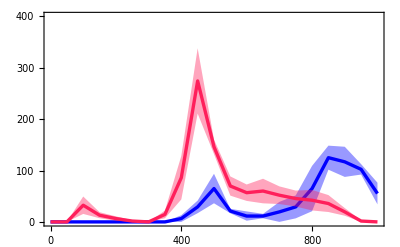

```mathematica
Show[ctG,ccG]
```